#### 1)

```mathematica
f=3/x^5-5/((x^9)^(1/5));
g=ArcSin[x]/5^x;
h=Sin[x]Cos[x^5];
D[f,x]
D[g,x]
D[h,x]
```

-15/x^6+(9 x^8)/((x^9)^(6/5))

5^-x/(√(1-x^2))-5^-x ArcSin[x] Log[5]

Cos[x] Cos[x^5]-5 x^4 Sin[x] Sin[x^5]

#### 2)

```mathematica
f=Sqrt[x];
Series[f,{x,4,2}]//Normal
%/.{x->4.2}
Sqrt[4.2]
```

2+1/4 (-4+x)-1/64 (-4+x)^2

2.04938

2.04939

#### 3)

72 x-18 x^2-8 x^3+3 x^4

72-36 x-24 x^2+12 x^3

{{x→2},{x→-√3},{x→√3}}

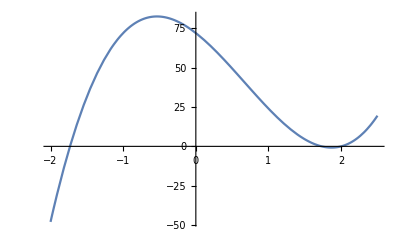

```mathematica
(x-2)(x^2-3)//Expand;
Integrate[%,x]12//Expand
D[%,x]
Solve[%==0,x]
Plot[%%,{x,-2,2.5}]
```

#### 4)

```mathematica
3/(x+2)-4/(x+2)^2//Together
Integrate[%,x]
```

(2+3 x)/(2+x)^2

4/(2+x)+3 Log[2+x]

#### 5)

```mathematica
Integrate[√x-1/x^2,{x,1,4}]
Integrate[x/Sqrt[3 x^2+4],{x,0,2}]
```

47/12

2/3

#### 6)

{{x→-1/2},{x→1}}

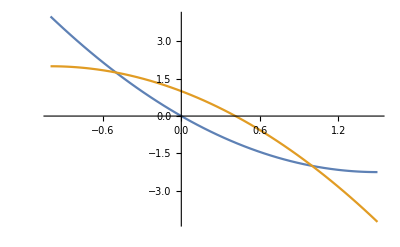

9/8

```mathematica
(x-1)(2x+1)//Expand;
y1=x^2-3x;
y2=-x^2-2x+1;
Solve[y1==y2,x]
Plot[{y1,y2},{x,-1,1.5}]
Integrate[y2-y1,{x,-1/2,1}]
```

#### 7)

1

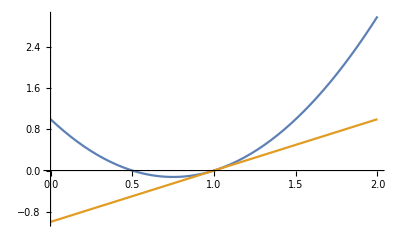

-1+x

```mathematica
f1[x_]:=2 x^2-3x+1;
f1'[1]
g1[x_]:=x-1+f1[1];
Plot[{f1[x],g1[x]},{x,0,2}]
g1[x]
```

#### 8)

```mathematica
y1=x^2;
y2=2x;
S=Integrate[(y2-y1),{x,0,2}]
Sy=Integrate[(y2-y1)x,{x,0,2}]
Sx=1/2Integrate[y2^2-y1^2,{x,0,2}]
```

4/3

4/3

32/15